# sac_test_Different_KA_SigmaXY

## initial tests

change KA from 1.0 to 0.0 does not change the behavior of SAC
change the simgaXY does !

```mathematica
test1=Import["/home/chengling/Research/Project/Cell/glassyDynamics/localTest/SACTest/SACtime_N64_p3.8500_T0.00003600_KA0.000_waitingTime100000_idx0.nc","Data"]
```

<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>

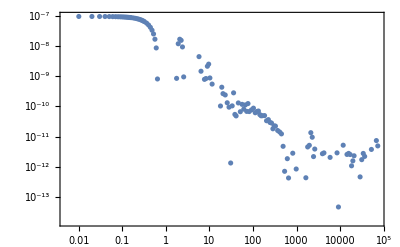

```mathematica
ListLogLogPlot[Table[{test1[[1,i]],test1[[2,i]]},{i,Length[test1[[1]]]}]]
```

```mathematica
test2=Import["/home/chengling/Research/Project/Cell/glassyDynamics/localTest/SACTest/SACtime_N256_p3.8500_T0.00020000_KA1.000_waitingTime10000_idx0.nc","Data"]
```

<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>

```mathematica
test2[[1,-1]]
```

9175.04

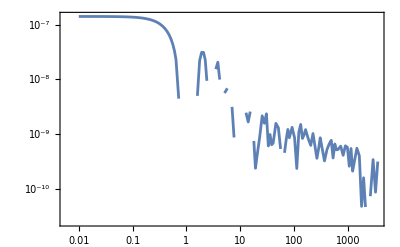

```mathematica
ListLogLogPlot[Table[{test2[[1,i]],test2[[2,i]]},{i,Length[test2[[1]]]}],Joined->True]
```

```mathematica
test3=Import["/home/chengling/Research/Project/Cell/glassyDynamics/localTest/SACTest/SACtime_N256_p3.8250_T0.00150000_KA0.000_waitingTime10000_idx0.nc","Data"]
```

<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>

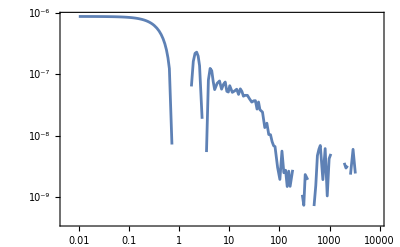

```mathematica
ListLogLogPlot[Table[{test3[[1,i]],test3[[2,i]]},{i,Length[test3[[1]]]}],Joined->True]
```

```mathematica
test3=Import["/home/chengling/Research/Project/Cell/3dVoronoi/data/bidisperse/N512/s5.500/stressAutoCorrelation_bidisperse_N512_s5.5000_T0.00150000_sizeRatio1.250_fraction0.800_idx0.nc","Data"]
```

<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>

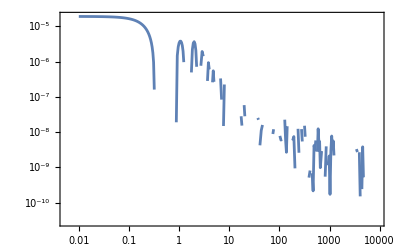

```mathematica
ListLogLogPlot[Table[{test3[[1,i]],test3[[2,i]]},{i,Length[test3[[1]]]}],Joined->True]
```

```mathematica
test3=Import["/home/chengling/Research/Project/Cell/glassyDynamics/localTest/SACTest/uniformStress_boundaryStress_N256_p3.8250_T0.00150000_KA1.000_idx0.nc","Data"]
```

<|/firstValue→NumericArray[<613644>, Real64],/secondValue→NumericArray[<613644>, Real64]|>

```mathematica
Mean[Normal[test3[[1]]]]
```

9.08502×10^-6

```mathematica
Mean[Normal[test3[[2]]]]
```

-6.3162×10^-6

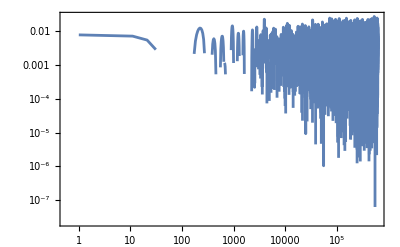

```mathematica
ListLogLogPlot[{Table[{i,-test3[[2,i]]},{i,1,Length[test3[[1]]],10}]},Joined->True]
```

```mathematica
Variance[Table[test3[[1,i]],{i,Length[test3[[1]]]}]]
```

9.826×10^-7

```mathematica
Variance[Table[test3[[2,i]]/8,{i,Length[test3[[1]]]}]]
```

6.12698×10^-7

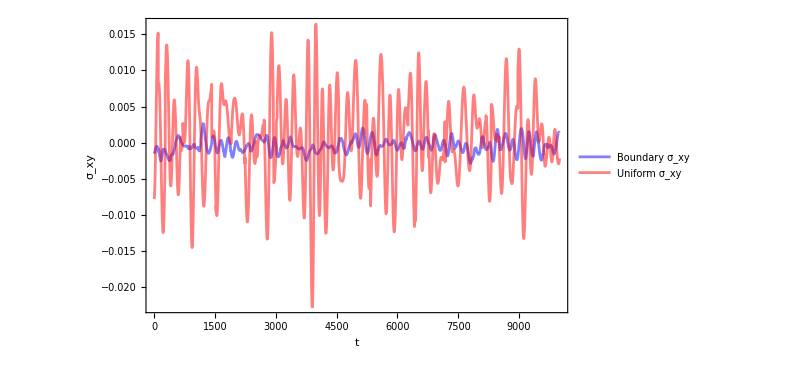

```mathematica
stressTrajectoryPlot=ListPlot[{Table[{i,test3[[1,i]]},{i,1,10000}],Table[{i,test3[[2,i]]},{i,1,10000}]},PlotLegends->{"Boundary σ_xy","Uniform σ_xy"},ImageSize->600,Joined->True,PlotStyle->{Directive[Blue,Opacity[0.5]],Directive[Red,Opacity[0.5]]},PlotRange->All,FrameLabel->{"t","σ_xy"}]
```

```mathematica
sacBoun=Import["/home/chengling/Research/Project/Cell/glassyDynamics/localTest/SACTest/SAC_boundarytime_N64_p3.8250_T0.00250000_KA1.000_waitingTime10000_idx0.nc","Data"]
```

<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>

```mathematica
ListLogLogPlot[Table[{sacBoun[[1,i]],sacBoun[[2,i]]},{i,Length[sacBoun[[1]]]}]]
```

```mathematica
sacNormal=Import["/home/chengling/Research/Project/Cell/glassyDynamics/localTest/SACTest/SACtime_N64_p3.8250_T0.00250000_KA1.000_waitingTime10000_idx0.nc","Data"]
```

<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>

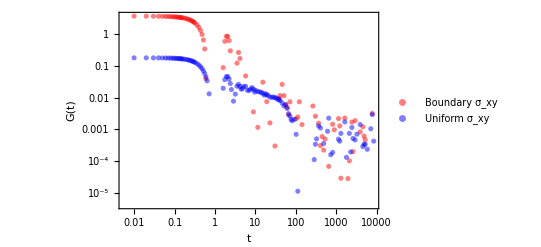

```mathematica
sacComparisonHighTPlot=ListLogLogPlot[{Table[{sacBoun[[1,i]],sacBoun[[2,i]]*64/0.0025},{i,Length[sacBoun[[1]]]}],Table[{sacNormal[[1,i]],sacNormal[[2,i]]*64/0.0025},{i,Length[sacNormal[[1]]]}]},PlotStyle->{Directive[Red,Opacity[0.5]],Directive[Blue,Opacity[0.5]]},ImageSize->400,FrameLabel->{"t","G(t)"},PlotLegends->{"Boundary σ_xy","Uniform σ_xy"}]
```

```mathematica
sacBoun=Import["/home/chengling/Research/Project/Cell/glassyDynamics/localTest/SACTest/SAC_boundarytime_N64_p3.8250_T0.00050000_KA1.000_waitingTime100000_idx0.nc","Data"]
```

<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>

```mathematica
ListLogLogPlot[Table[{sacBoun[[1,i]],sacBoun[[2,i]]},{i,Length[sacBoun[[1]]]}]]
```

```mathematica
sacNormal=Import["/home/chengling/Research/Project/Cell/glassyDynamics/localTest/SACTest/SACtime_N64_p3.8250_T0.00050000_KA1.000_waitingTime100000_idx0.nc","Data"]
```

<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>

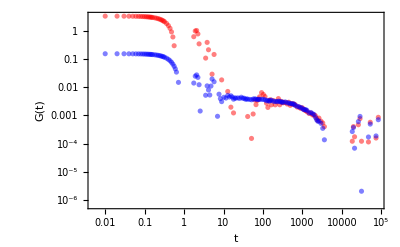

```mathematica
sacComparisonLowTPlot=ListLogLogPlot[{Table[{sacBoun[[1,i]],sacBoun[[2,i]]*64/0.0005},{i,Length[sacBoun[[1]]]}],Table[{sacNormal[[1,i]],sacNormal[[2,i]]*64/0.0005},{i,Length[sacNormal[[1]]]}]},PlotStyle->{Directive[Red,Opacity[0.5]],Directive[Blue,Opacity[0.5]]},ImageSize->400,FrameLabel->{"t","G(t)"}]
```

## SAC for p0=3.825 N=64

```mathematica
temperatures={0.0031,0.0025, 0.002 ,0.0015, 0.001 ,0.00067, 0.0005}
```

{0.0031,0.0025,0.002,0.0015,0.001,0.00067,0.0005}

```mathematica
tauList={120., 200., 300. ,1000, 1500 ,5000 ,10000}
```

{120.,200.,300.,1000,1500,5000,10000}

```mathematica
tauEstimate[t_]:=If[t<=1000,10000,10*t]
```

```mathematica
tauEstimate[tauList[[6]]]
```

{0,1000,10000.,15000.,20000.,25000.,30000.,35000.,40000.,45000.}

```mathematica
test=Import["/home/chengling/Research/Project/Cell/glassyDynamics/localTest/SACTest/SAC_boundarytime_N64_p3.8250_T0.00067000_KA1.000_waitingTime50000_idx0.nc"]
```

{/firstValue,/secondValue}

```mathematica
sacUniform=Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/localTest/SACTest/SACtime_N64_p3.8250_T","_KA1.000_waitingTime","_idx0.nc"},{temperatures[[T]],tauEstimate[tauList[[T]]]},{8,0}],"Data"],{T,Length[temperatures]}];
```

```mathematica
sacBoundary=Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/localTest/SACTest/SAC_boundarytime_N64_p3.8250_T","_KA1.000_waitingTime","_idx0.nc"},{temperatures[[T]],tauEstimate[tauList[[T]]]},{8,0}],"Data"],{T,Length[temperatures]}];
```

```mathematica
Subscript[σ, xy]
```

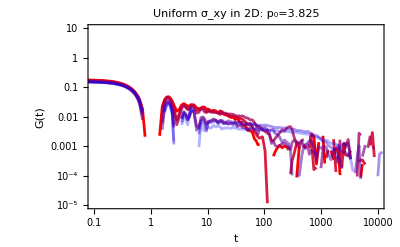

```mathematica
sac2DUniformPlot=Show[ListLogLogPlot[Table[Table[{Normal[sacUniform[[T,1]]][[rec]],Normal[sacUniform[[T,2]]][[rec]]/temperatures[[T]]*64},{rec,Length[sacUniform[[T,2]]]}],{T,Length[temperatures]}],PlotRange->{{0.1,10000},{0.00001,10}},Joined->True,FrameLabel->{"t","G(t)"},PlotLabel->"Uniform σ_xy in 2D: p_0=3.825",ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperatures]]]]
```

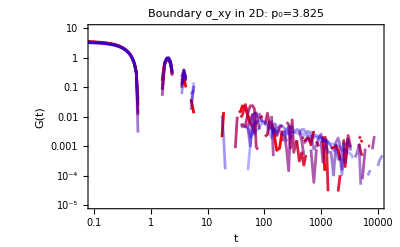

```mathematica
sac2DBoundaryPlot=Show[ListLogLogPlot[Table[Table[{Normal[sacBoundary[[T,1]]][[rec]],Normal[sacBoundary[[T,2]]][[rec]]/temperatures[[T]]*64},{rec,Length[sacBoundary[[T,2]]]}],{T,Length[temperatures]}],PlotRange->{{0.1,10000},{0.00001,10}},Joined->True,FrameLabel->{"t","G(t)"},PlotLabel->"Boundary σ_xy in 2D: p_0=3.825",ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperatures]]]]
```

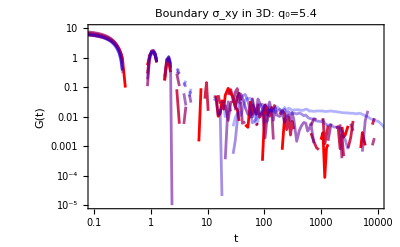
```mathematica
sac3DBoundaryPlot=-Graphics-;
```

```mathematica
Export["/home/chengling/Research/updates/2025_06_09/sacComparision.jpeg",Grid[Partition[Flatten[{sac2DBoundaryPlot,sac3DBoundaryPlot,sac2DBoundaryPlot,sac2DUniformPlot}],2]],ImageResolution->200];
```

```mathematica
Export["/home/chengling/Research/updates/2025_06_09/sacComparisionIndividual.jpeg",Grid[Partition[Flatten[{sacComparisonLowTPlot,sacComparisonHighTPlot}],2]],ImageResolution->200];
```

```mathematica
Export["/home/chengling/Research/updates/2025_06_09/stressTrajectoryPlot.jpeg",stressTrajectoryPlot,ImageResolution->200];
```